```mathematica
data1=Import[NotebookDirectory[]<>"/LOCAL DENSITY HISTOGRAMS (Iter = 1).xls","xls"][[1]];
data2=Import[NotebookDirectory[]<>"/LOCAL DENSITY HISTOGRAMS (Iter = 2).xls","xls"][[1]];
```

```mathematica
data1cols=Dimensions[data1][[2]];
data2cols=Dimensions[data2][[2]];
```

```mathematica
data1filt=Table[MapThread[{#1,#2}&,{data1[[2;;All,i]],LowpassFilter[data1[[2;;All,i+1]],0.05]}],{i,1,data1cols,2}];
data2filt=Table[MapThread[{#1,#2}&,{data2[[2;;All,i]],LowpassFilter[data2[[2;;All,i+1]],0.02]}],{i,1,data2cols,2}];
```

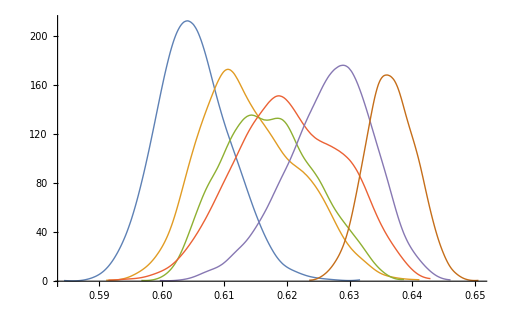

```mathematica
ListLinePlot[data1filt,PlotStyle->Thick]
```

```mathematica
Export[NotebookDirectory[]<>"/LOCAL_DENSITY_HISTOGRAMS_FILTER (Iter = 1).xlsx",data1filt];
Export[NotebookDirectory[]<>"/LOCAL_DENSITY_HISTOGRAMS_FILTER (Iter = 2).xlsx",data2filt];
```

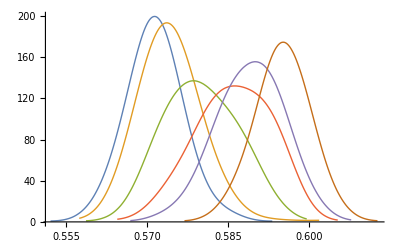

```mathematica
ListLinePlot[data2filt,PlotStyle->Thick]
```